### Analytic Expression

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=1/16(202/3-20/9 Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3 Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-(8β0[Nf])/(2(4π)^2);
b1[Nf_]=-(32 β1[Nf])/(2(4π)^2);

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+1/(β0[Nf]^7 t^4)( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √a4t[Log[μ^2/ΛQCD^2]]; 
mDcal[μ_,T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ];
mDcalT[μ_,T_,c_,d_]:=1/T mDcal[μ,T,c,d];
mDcalTT[T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g[2π T,T]T+1/(4π)Nc g[2π T,T]^2 T Log[Sqrt[Nc/3+nF/6]/g[2π T,T]]+c g[2π T,T]^2 T+d g[2 π T,T]^3 T ];
```

NDSolve::precw: The precision of the differential equation ({{as'[t]==1/12 as[t]^2 (-33.+2 If[«3»])+1/96 as[t]^3 (-612.+76. If[«3»])+1/128 as[t]^4 (-2857+5033/9 If[«3»]-325/27 Power[«2»])+1/256 as[t]^5 (-149753/6-1093/729 Power[«2»]-3564 Zeta[«1»]-Power[«2»] Plus[«2»]+If[«3»] Plus[«2»]),as[10000 Log[4]]==0.0000376185},{},{},{},{}}) is less than WorkingPrecision (32.).

NDSolve::ndsz: At t == 2.05914, step size is effectively zero; singularity or stiff system suspected.

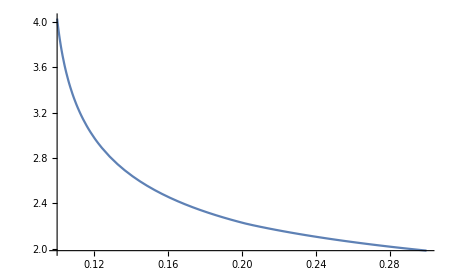

```mathematica
Plot[g4[2 π x],{x,0.1,0.3},PlotRange->All]
```

```mathematica
g4inv=Quiet[Table[{y,FindRoot[g4[2 π x]==y,{x,0.1}][[1,2]]},{y,2,4,0.01}]];
```

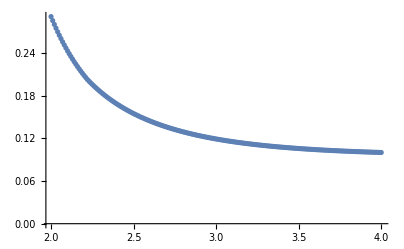

```mathematica
ListPlot[g4inv]
```

```mathematica
inter=Interpolation[g4inv];
```

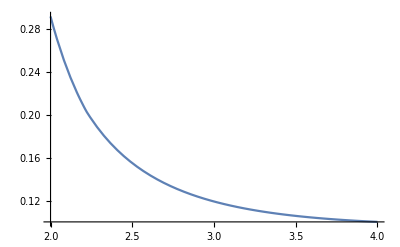

```mathematica
Plot[inter[x],{x,2,4}]
```

```mathematica
kfinalu={0.8016955527941704,-0.36040626803845205};
kfinall={0.1389898610341079,-0.14922900812090412};
kfinal={0.47034270691413915,-0.25481763807967805};(*100k run*)
kerror={kfinalu[[1]]-kfinal[[1]],kfinal[[2]]-kfinalu[[2]]};
kAR={0.84,-0.4};
```

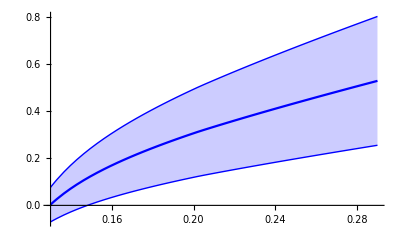

```mathematica
Plot[{mDcal[2π,x,kfinal[[1]],kfinal[[2]]],mDcal[2π,x,kfinal[[1]]+1.96 kerror[[1]],kfinal[[2]]-1.96 kerror[[2]]],mDcal[2π,x,kfinal[[1]]-1.96 kerror[[1]],kfinal[[2]]+1.96 kerror[[2]]]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}]
```

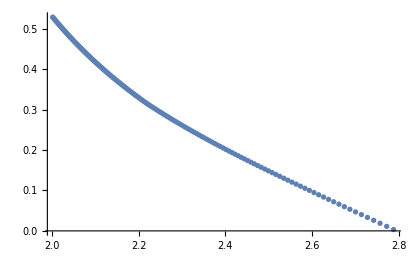

```mathematica
ListPlot[Table[{g4[2 π x],mDcal[2π,x,kfinal[[1]],kfinal[[2]]]},{x,0.13,0.29,0.001}]]
```

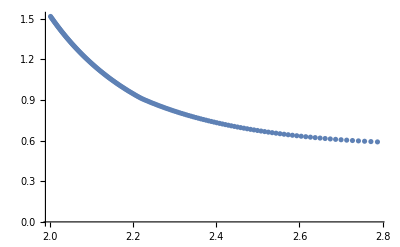

```mathematica
ListPlot[Table[{g4[2 π x],mDc[2π x,x,0.]},{x,0.13,0.29,0.001}]]
```

```mathematica
inter1=Interpolation[Table[{g4[2 π x],mDcal[2π,x,kfinal[[1]],kfinal[[2]]]},{x,0.13,0.29,0.001}]];
```

```mathematica
mDc[k_,T_,μ_]:=(Nc+nf[k]/2)g4[k]^2 T^2+nf[k]/(2 π^2)g4[k]^2 μ^2;
gm1[k_,T_,μ_]:=g4[k]/(1+mDc[k,T,μ]/k^2);
```

```mathematica
mDc[2π Tc,Tc,0.2]
```

0.713156

```mathematica
gm1[2π Tc,Tc,0.1]
```

1.45135

InterpolatingFunction::dmval: Input value {1.45983} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.45975} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.45949} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

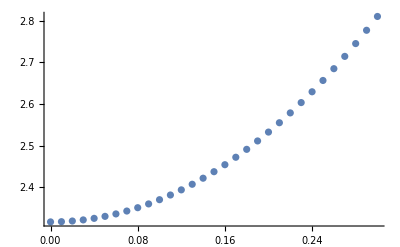

```mathematica
ListPlot[Table[{x,inter1[gm1[2π Tc,Tc,x]]},{x,0.,0.3,0.01}]]
```

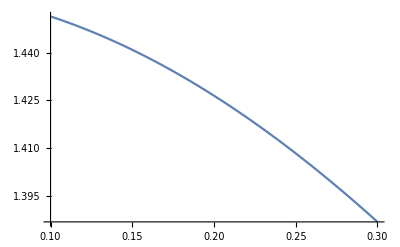

```mathematica
Plot[gm1[2π Tc,Tc,x],{x,0.1,0.3}]
```

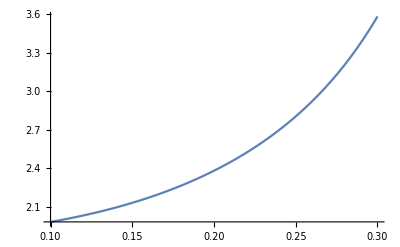

```mathematica
Plot[gm[2π Tc,Tc,x],{x,0.1,0.3}]
```

```mathematica
T={0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861};
```

```mathematica
mdfitrandfinal={{0.038919565918040445,0.06743682653727344},{0.12582094383686163,0.10923208048614581},{0.1892583277055926,0.12852782269560006},{0.30988003094936495,0.18358091276753688},{0.48025965960625705,0.1479696311077649},{0.49657169002278573,0.1791783591997105},{0.6465066249674667,0.1798587912586749}};(*10k run*)
```

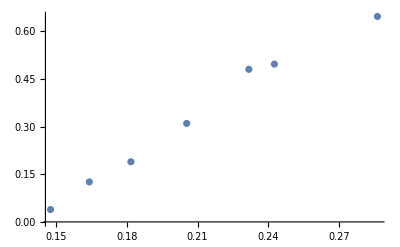

```mathematica
ListPlot[Transpose[{T,mdfitrandfinal[[All,1]]}]]
```

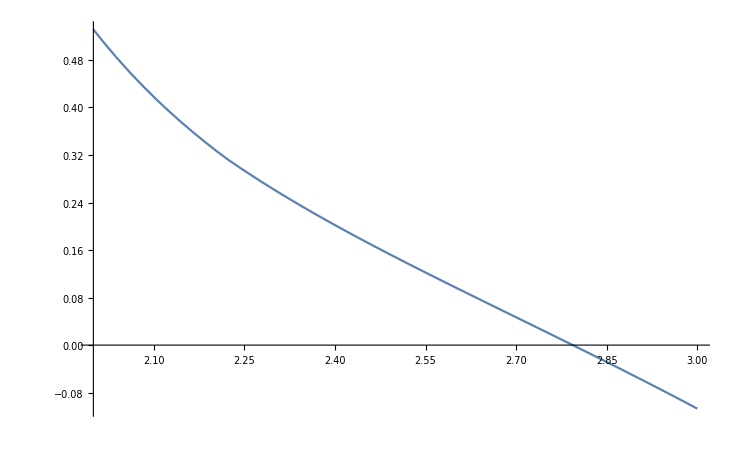

```mathematica
Plot[mDcal[2π,inter[x],kfinal[[1]],kfinal[[2]]],{x,2,3.}]
```

```mathematica
Λgb=Exp[-EulerGamma-1/2 Log[3/8]+1/44];
Λg[T_]:=2π T Λgb;
Λfb=Exp[-EulerGamma+1/2];
Λf[T_]:=π T Λfb;
```

```mathematica
g[k_,T_]:=g4[k]/(1+g4[k]/(12π)(11Nc Log[Λg[T]^2/k^2]-2nf[k] Log[Λf[T]^2/k^2]))
```

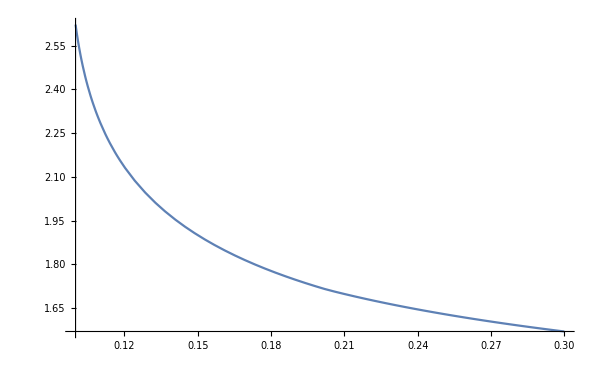

```mathematica
Plot[g[2π T,T],{T,0.1,0.3}]
```

```mathematica
ginv=Quiet[Table[{y,FindRoot[g[2 π x,x]==y,{x,0.1}][[1,2]]},{y,1.5,2.7,0.01}]];
```

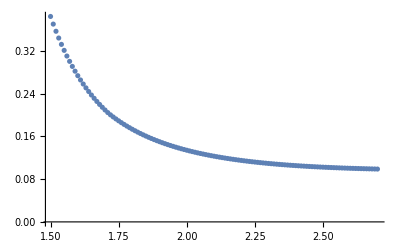

```mathematica
ListPlot[ginv]
```

```mathematica
ginter=Interpolation[ginv];
```

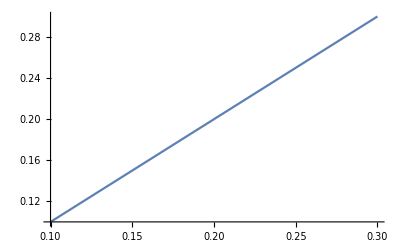

```mathematica
Plot[ginter[g[2π x,x]],{x,0.1,0.3}]
```

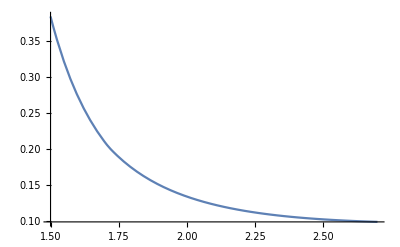

```mathematica
Plot[ginter[x],{x,1.5,2.7}]
```

InterpolatingFunction::dmval: Input value {2.72221} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.75429} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.78578} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

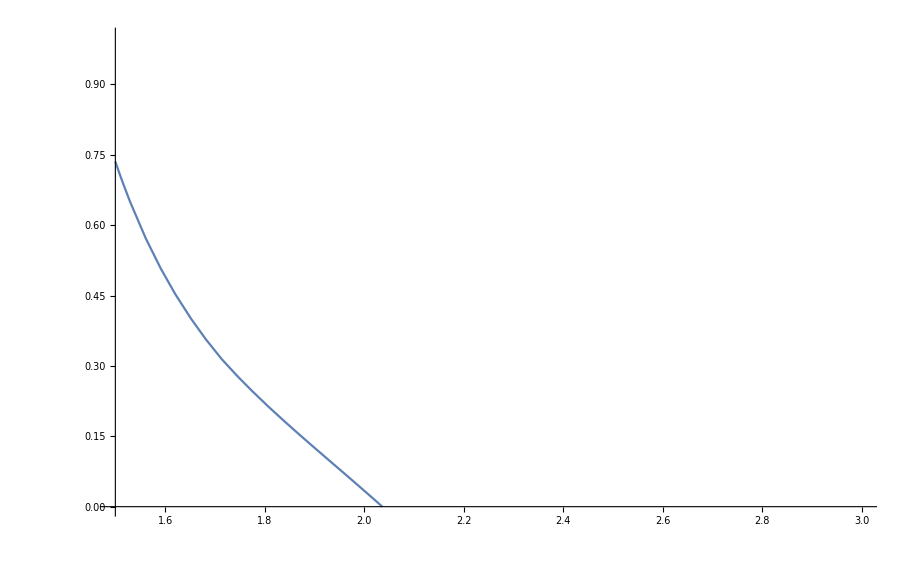

```mathematica
Plot[mDcal[2π,ginter[x],kfinal[[1]],kfinal[[2]]],{x,1.5,3.},PlotRange->{0.,1}]
```

```mathematica
g[2π 0.17,0.17]
```

1.81242

```mathematica
mDcal[2π,0.17,kfinal[[1]],kfinal[[2]]]
```

0.208616

```mathematica
βf=(7 Zeta[3])/(2 π^2);
Λfm[T_,μ_]:= Exp[βf/2 μ^2/T^2]Λf[T];
```

```mathematica
gm[k_,T_,μ_]:=g4[k]/(1+g4[k]/(12π)(11Nc Log[Λg[T]^2/k^2]-2nf[k] Log[Λfm[T,μ]^2/k^2]))
```

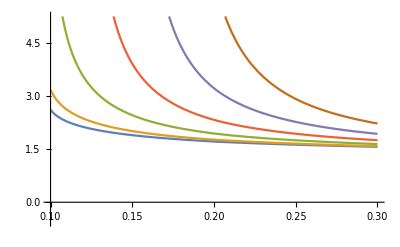

```mathematica
Plot[{gm[2π T,T,0.],gm[2π T,T,0.1],gm[2π T,T,0.2],gm[2π T,T,0.3],gm[2π T,T,0.4],gm[2π T,T,0.5]},{T,0.1,0.3}]
```

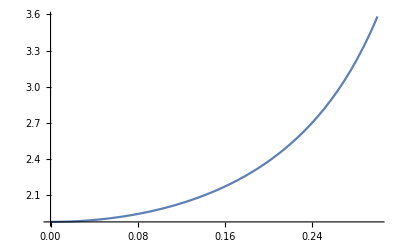

```mathematica
Tc=0.155;
Plot[gm[2π Tc,Tc,x],{x,0.,0.3}]
```

```mathematica
gm[2π Tc,Tc,0.1]
```

1.98038

```mathematica
chemD=Table[{x,mDcal[2π,ginter[gm[2π Tc,Tc,x]],kfinal[[1]],kfinal[[2]]]},{x,0.,0.3,0.01}]
```

InterpolatingFunction::dmval: Input value {2.80349} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.92145} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.05503} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.,0.14846},{0.01,0.147537},{0.02,0.144766},{0.03,0.140137},{0.04,0.133636},{0.05,0.125234},{0.06,0.114892},{0.07,0.102547},{0.08,0.0881087},{0.09,0.0714493},{0.1,0.0523898},{0.11,0.030684},{0.12,0.00599708},{0.13,-0.0221232},{0.14,-0.0542849},{0.15,-0.0913037},{0.16,-0.134276},{0.17,-0.184682},{0.18,-0.244528},{0.19,-0.31656},{0.2,-0.404576},{0.21,-0.51389},{0.22,-0.652046},{0.23,-0.82994},{0.24,-1.06362},{0.25,-1.37861},{0.26,-1.84792},{0.27,-3.01657},{0.28,3.46019×10^34},{0.29,4.16394×10^36},{0.3,8.76664×10^37}}